# f.figure.rencon2.strange.baryons-all.merge.nb

```mathematica
NotebookFileName[]
```

C:\octet.formfactor\f.figure.rencon2.strange.baryons-all.merge.nb

this nb is to record the all baryon octets ge gm experiment data and calculated data.

## initial

```mathematica
Needs["ErrorBarPlots`"]
```

ge`charge: octet: 1 3 4 6, line, dash, dot, dot-dash

ge`neutral: octet: 2 5 7 8, line, dash, dot, dot-dash

** ** ** ** ** ** ** ** ** ** ** **

gm/μm`charge: octet: 1 3 4 6, line, dash, dot, dot-dash

gm/μm`neutral: octet: 2 5 7 8, line, dash, dot, dot-dash

```mathematica
directory`fig=FileNameJoin[{NotebookDirectory[],"/expression-fig/"}]
```

C:\octet.formfactor\expression-fig

## normal

## style

```mathematica
style`exp={
AbsoluteThickness[_]-> AbsoluteThickness[.8],
PointSize[_]->PointSize[0.02]
};
```

```mathematica
style`calc={
AbsoluteThickness[_]->AbsoluteThickness[.8]
};
```

```mathematica
fig`calc`baryons`ge`total=Get[
FileNameJoin[{directory`fig,
"fig.calc.baryons.ge.tot.L-0.90.ci-1.0.m"
}
]
]/.style`calc;
```

```mathematica
fig`calc`baryons`gm`total=Get[
FileNameJoin[{directory`fig,
"fig.calc.baryons.gm.tot.L-0.90.ci-1.0.m"
}
]
]/.style`calc;
```

```mathematica
fig`calc`baryons`ge`total//Dimensions
```

{8,3}

```mathematica
color`default=RGBColor[0.368417, 0.506779, 0.709798];
```

给定颜色和线型方案，带电粒子4个，中性粒子4个，同样的排列

```mathematica
style`octet={
{color`default->Blue},
{Line[x_]:>{Dashing[Medium],Line[x]},color`default->Red},
{Line[x_]:>{Dotted,Line[x]},color`default->Green},
{Line[x_]:>{DotDashed,Line[x]},color`default->Brown}
};
```

```mathematica
style`legend={
Directive[Dashing[1],Blue],
Directive[Dashing[Medium],Red],
Directive[Dotted,Green],
Directive[DotDashed,Brown]
};
```

## draw

## initial

```mathematica
style`frame={
{
Directive[AbsoluteThickness[0.8],FontSize->7,Black],
Directive[AbsoluteThickness[0.8],FontSize->7,Black]
},
{
Directive[AbsoluteThickness[0.8],FontSize->7,Black],
Directive[AbsoluteThickness[0.8],FontSize->7,Black]
}
};
```

```mathematica
fontsize`frame=8;
imagesize=Scaled[.6];
```

```mathematica
fig`legend`magni=0.5;
```

## ge`charge

ge`charge: octet: 1 3 4 6, line, Dashing, Dotted, DotDashed

fig`calc`baryons`ge`total⟦octet,tree-loop-total⟧

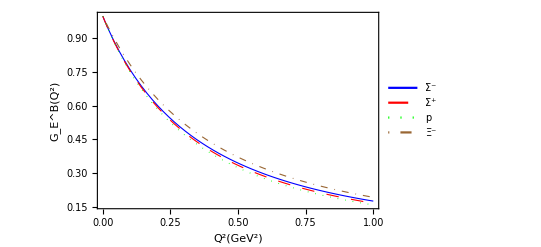

```mathematica
fig`baryons`ge`charge=
Legended[
fig`test=Show[
fig`test2=fig`calc`baryons`ge`total⟦1,3⟧/.style`octet⟦1⟧,
fig`calc`baryons`ge`total⟦3,3⟧/.style`octet⟦2⟧,
fig`calc`baryons`ge`total⟦4,3⟧/.style`octet⟦3⟧,
fig`calc`baryons`ge`total⟦6,3⟧/.style`octet⟦4⟧,
PlotRange->Full,
PlotRangePadding->{{0,0},{Scaled[0.09],Scaled[0.09]}},
Frame->True,
FrameStyle->style`frame,
FrameLabel->{
{Style["G_E^B(Q^2)",FontFamily->"Times New Roman",FontSize->fontsize`frame],None},
{Style["Q^2(GeV^2)",FontFamily->"Times New Roman",FontSize->fontsize`frame],None}
}
],
(*++++++++++++++++++++++++++++++*)
Placed[
Style[
LineLegend[{
style`legend⟦1⟧,style`legend⟦2⟧,
style`legend⟦3⟧,style`legend⟦4⟧
},
Style[#1,FontFamily->"Times New Roman",FontSize->12]&/@
{"Σ^-","Σ^+","p","Ξ^-"}
(*,LegendFunction->Framed*)
],
Magnification->fig`legend`magni
],
{
{0.03,0.03},
{0.,0.}
}
]
]
```

## ge`neutral

ge`neutral: octet: 2 5 7 8, line, Dashing, Dotted, DotDashed

fig`calc`baryons`ge`total⟦octet,tree-loop-total⟧

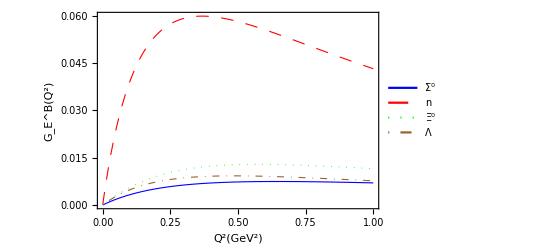

```mathematica
fig`baryons`ge`neutral=
Legended[
Show[
fig`calc`baryons`ge`total⟦2,3⟧/.style`octet⟦1⟧,
fig`calc`baryons`ge`total⟦5,3⟧/.style`octet⟦2⟧,
fig`calc`baryons`ge`total⟦7,3⟧/.style`octet⟦3⟧,
fig`calc`baryons`ge`total⟦8,3⟧/.style`octet⟦4⟧,
PlotRange->Full,
PlotRangePadding->{{0,0},{Scaled[0.09],Scaled[0.09]}},
Frame->True,
FrameStyle->style`frame,
FrameLabel->{
{Style["G_E^B(Q^2)",FontFamily->"Times New Roman",FontSize->fontsize`frame],None},
{Style["Q^2(GeV^2)",FontFamily->"Times New Roman",FontSize->fontsize`frame],None}
}
],
(*++++++++++++++++++++++++++++++*)
Placed[
Style[
LineLegend[{
style`legend⟦1⟧,style`legend⟦2⟧,
style`legend⟦3⟧,style`legend⟦4⟧
},
Style[#1,FontFamily->"Times",FontSize->12]&/@
{"Σ^0","n","Ξ^0","Λ"}
(*,LegendFunction->Framed*)
],
Magnification->fig`legend`magni
],
{
{0.7,0.3},
{0.,0.}
}
]
]
```

*********************************************************

## gm`charge

gm`charge: octet: 1 3 4 6, line, Dashing, Dotted, DotDashed

fig`calc`baryons`ge`total⟦octet,tree-loop-total⟧

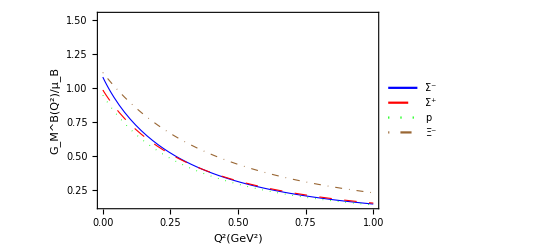

```mathematica
fig`baryons`gm`charge=
Legended[
Show[
fig`calc`baryons`gm`total⟦1,3⟧/.style`octet⟦1⟧,
fig`calc`baryons`gm`total⟦3,3⟧/.style`octet⟦2⟧,
fig`calc`baryons`gm`total⟦4,3⟧/.style`octet⟦3⟧,
fig`calc`baryons`gm`total⟦6,3⟧/.style`octet⟦4⟧,
PlotRange->Full,
PlotRangePadding->{{0,0},{Scaled[0.09],Scaled[0.09]}},
Frame->True,
FrameStyle->style`frame,
FrameLabel->{
{Style["G_M^B(Q^2)/μ_B",FontFamily->"Times New Roman",FontSize->fontsize`frame],None},
{Style["Q^2(GeV^2)",FontFamily->"Times New Roman",FontSize->fontsize`frame],None}
}
],
(*++++++++++++++++++++++++++++++*)
Placed[
Style[
LineLegend[{
style`legend⟦1⟧,style`legend⟦2⟧,
style`legend⟦3⟧,style`legend⟦4⟧
},
Style[#1,FontFamily->"Times",FontSize->12]&/@
{"Σ^-","Σ^+","p","Ξ^-"}
(*,LegendFunction->Framed*)
],
Magnification->fig`legend`magni
],
{
{0.03,0.03},
{0.,0.}
}
]
]
```

## gm`neutral

gm`neutral: octet: 2 5 7 8, line, Dashing, Dotted, DotDashed

fig`calc`baryons`ge`total⟦octet,tree-loop-total⟧

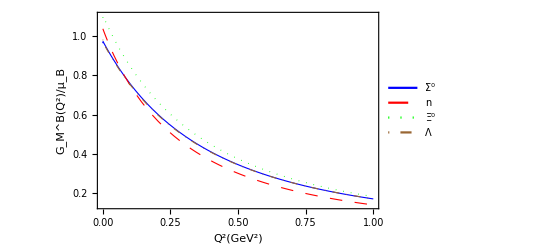

```mathematica
fig`baryons`gm`neutral=
Legended[
Show[
fig`calc`baryons`gm`total⟦2,3⟧/.style`octet⟦1⟧,
fig`calc`baryons`gm`total⟦5,3⟧/.style`octet⟦2⟧,
fig`calc`baryons`gm`total⟦7,3⟧/.style`octet⟦3⟧,
fig`calc`baryons`gm`total⟦8,3⟧/.style`octet⟦4⟧,
PlotRange->Full,
PlotRangePadding->{{0,0},{Scaled[0.09],Scaled[0.09]}},
Frame->True,
FrameStyle->style`frame,
FrameLabel->{
{Style["G_M^B(Q^2)/μ_B",FontFamily->"Times New Roman",FontSize->fontsize`frame],None},
{Style["Q^2(GeV^2)",FontFamily->"Times New Roman",FontSize->fontsize`frame],None}
}
],
(*++++++++++++++++++++++++++++++*)
Placed[
Style[
LineLegend[{
style`legend⟦1⟧,style`legend⟦2⟧,
style`legend⟦3⟧,style`legend⟦4⟧
},
Style[#1,FontFamily->"Times",FontSize->12]&/@
{"Σ^0","n","Ξ^0","Λ"}
(*,LegendFunction->Framed*)
],
Magnification->fig`legend`magni
],
{
{0.7,0.3},
{0.,0.}
}
]
]
```

## export

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],"/expression-results/"}]]
```

C:\octet.formfactor\expression-results

```mathematica
Export["fig`baryons`ge`charge.pdf",fig`baryons`ge`charge];
Export["fig`baryons`ge`neutral.pdf",fig`baryons`ge`neutral];
```

```mathematica
Export["fig`baryons`gm`charge.pdf",fig`baryons`gm`charge];
Export["fig`baryons`gm`neutral.pdf",fig`baryons`gm`neutral];
```